```mathematica
Directory[]
```

C:\Users\chuck.WHITMER\Documents

```mathematica
SetDirectory["c:\\Users\\chuck.WHITMER\\Documents\\FUSOR"]
```

c:\Users\chuck.WHITMER\Documents\FUSOR

```mathematica
theList=Import["listForDrWhitmerFinal.txt","table"];
```

```mathematica
Dimensions[theList]
```

{1000,3}

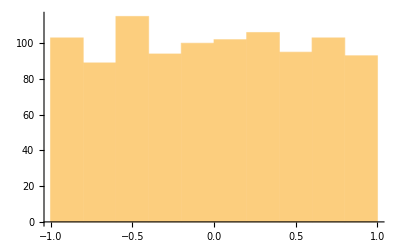

```mathematica
Histogram[Cos /@ theList[[All,1]]]
```

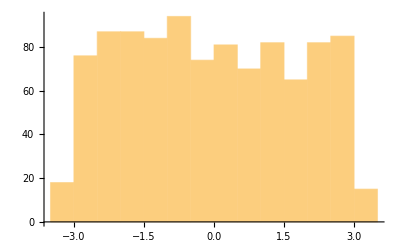

```mathematica
Histogram[theList[[All,2]]]
```

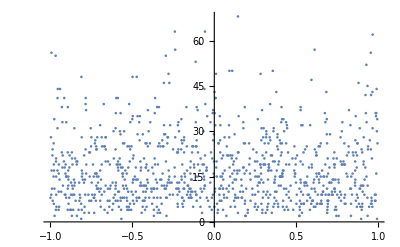

```mathematica
ListPlot[{Cos[#[[1]]],#[[3]]}&/@theList]
```

```mathematica
bins=Range[-1,1,2/10]
```

{-1,-4/5,-3/5,-2/5,-1/5,0,1/5,2/5,3/5,4/5,1}

```mathematica
binnedLists=Table[Select[theList,bins[[i]]≤Cos[#[[1]]]<bins[[i+1]]&][[All,3]],{i,Length[bins]-1}];
```

```mathematica
StandardError[ll_]:=StandardDeviation[ll]/Sqrt[Length[ll]]
```

```mathematica
binnedMeans=Around[Mean[#],StandardError[#]]&/@binnedLists
```

{16.91.1,16.41.0,17.01.0,19.61.3,18.51.2,18.21.2,17.41.0,16.21.0,14.90.9,19.61.4}

```mathematica
binCenters=1/2(Drop[bins,1]+Drop[bins,-1]);
```

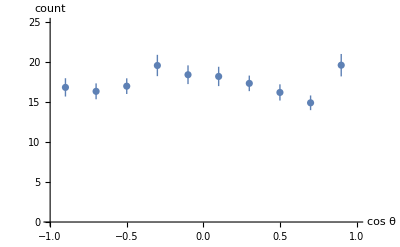

```mathematica
ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,25}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}]
```

```mathematica
GetAngles[x_,y_,z_]:={z/(√(x^2+y^2+z^2)),ArcTan[x,y]}
```

```mathematica
GetIdxFromLm[ll_,mm_]:=(ll+1)^2+mm-ll;
```

```mathematica
Table[GetIdxFromLm[l,m],{l,0,3},{m,-l,l}]
```

{{1},{2,3,4},{5,6,7,8,9},{10,11,12,13,14,15,16}}

```mathematica
GetLmFromIdx[idx_]:=Module[{l,m},
l=Floor[Sqrt[idx-1]];
m=idx-(l^2+l+1);
{l,m}]
```

```mathematica
Table[GetLmFromIdx[i],{i,16}]
```

{{0,0},{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2},{3,-3},{3,-2},{3,-1},{3,0},{3,1},{3,2},{3,3}}

```mathematica
alm=Table[Module[{l,m},{l,m}=GetLmFromIdx[idx];Total[Conjugate[SphericalHarmonicY[l,m,#[[1]],#[[2]]]]#[[3]]&/@theList]],{idx,49}](4 π)/Length[theList]
```

{61.848,-1.03692-0.641922 ⅈ,-0.523081,1.03692-0.641922 ⅈ,0.520032-1.0588 ⅈ,-0.589213-2.42883 ⅈ,-1.07313,0.589213-2.42883 ⅈ,0.520032+1.0588 ⅈ,1.0531+0.548043 ⅈ,-0.344302-1.99939 ⅈ,1.70437-3.57797 ⅈ,1.48319,-1.70437-3.57797 ⅈ,-0.344302+1.99939 ⅈ,-1.0531+0.548043 ⅈ,-4.51801-3.04371 ⅈ,-0.138737+0.804038 ⅈ,0.550107-0.859398 ⅈ,-0.213367+0.698233 ⅈ,5.84335,0.213367+0.698233 ⅈ,0.550107+0.859398 ⅈ,0.138737+0.804038 ⅈ,-4.51801+3.04371 ⅈ,-0.0734322+1.63149 ⅈ,-1.65847+1.04484 ⅈ,-0.715401-1.22652 ⅈ,-0.802814+0.595405 ⅈ,-2.20243+1.34304 ⅈ,-0.0141445,2.20243+1.34304 ⅈ,-0.802814-0.595405 ⅈ,0.715401-1.22652 ⅈ,-1.65847-1.04484 ⅈ,0.0734322+1.63149 ⅈ,0.375-1.4818 ⅈ,-2.07577+1.96809 ⅈ,1.14153-0.261051 ⅈ,1.26839-0.848414 ⅈ,-3.57339+0.284159 ⅈ,1.09905-0.742251 ⅈ,3.71255,-1.09905-0.742251 ⅈ,-3.57339-0.284159 ⅈ,-1.26839-0.848414 ⅈ,1.14153+0.261051 ⅈ,2.07577+1.96809 ⅈ,0.375+1.4818 ⅈ}

```mathematica
al0even=Table[Total[Conjugate[SphericalHarmonicY[l,0,#[[1]],#[[2]]]]#[[3]]&/@theList],{l,0,10,2}](4 π)/Length[theList]
```

{61.848,-1.07313,5.84335,3.71255,-1.10851,-1.3333}

```mathematica
alm[[1]]SphericalHarmonicY[0,0,π/2,0]
```

3.238

```mathematica
Mean[theList[[All,3]]]//N
```

3.238

```mathematica
SphericalHarmonicY[1,-1,θ,ϕ]/.Sin[θ]->y
```

1/2 ⅇ^(-ⅈ ϕ) √(3/(2 π)) y

```mathematica
SphericalHarmonicY[1,1,θ,ϕ]/.Sin[θ]->y
```

-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) y

```mathematica
f0[θ_]:=Sum[Module[{idx},idx=GetIdxFromLm[ll,0];alm[[idx]]SphericalHarmonicY[ll,0,θ,0]],{ll,0,0}]
```

```mathematica
f1[θ_]:=Sum[Module[{idx},idx=GetIdxFromLm[ll,0];alm[[idx]]SphericalHarmonicY[ll,0,θ,0]],{ll,0,1}]
```

```mathematica
f2[θ_]:=Sum[Module[{idx},idx=GetIdxFromLm[ll,0];alm[[idx]]SphericalHarmonicY[ll,0,θ,0]],{ll,0,2}]
```

```mathematica
f3[θ_]:=Sum[Module[{idx},idx=GetIdxFromLm[ll,0];alm[[idx]]SphericalHarmonicY[ll,0,θ,0]],{ll,0,3}]
```

```mathematica
f4[θ_]:=Sum[Module[{idx},idx=GetIdxFromLm[ll,0];alm[[idx]]SphericalHarmonicY[ll,0,θ,0]],{ll,0,4}]
```

```mathematica
f6[θ_]:=Sum[Module[{idx},idx=GetIdxFromLm[ll,0];alm[[idx]]SphericalHarmonicY[ll,0,θ,0]],{ll,0,6}]
```

```mathematica
g4[θ_]:=Sum[Module[{idx},idx=GetIdxFromLm[ll,0];alm[[idx]]SphericalHarmonicY[ll,0,θ,0]],{ll,0,4,2}]
```

```mathematica
g6[θ_]:=Sum[Module[{idx},idx=GetIdxFromLm[ll,0];alm[[idx]]SphericalHarmonicY[ll,0,θ,0]],{ll,0,6,2}]
```

```mathematica
h10[θ_]:=Sum[al0even[[ll/2+1]]SphericalHarmonicY[ll,0,θ,0],{ll,0,10,2}]
```

```mathematica
h6[θ_]:=Sum[al0even[[ll/2+1]]SphericalHarmonicY[ll,0,θ,0],{ll,0,6,2}]
```

```mathematica
f1[x]
```

```mathematica
3.238-0.10630702145235468 Cos[x]
```

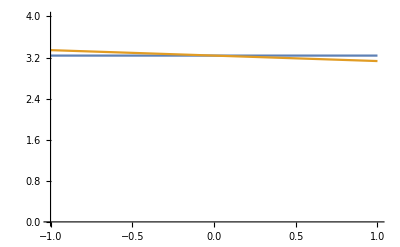

```mathematica
Plot[{f0[ArcCos[t]],f1[ArcCos[t]]},{t,-1,1},PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0}]
```

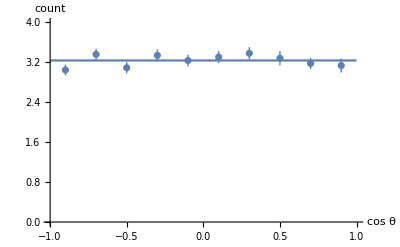

```mathematica
Show[ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}],
Plot[f0[ArcCos[t]],{t,-1,1},PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0}]]
```

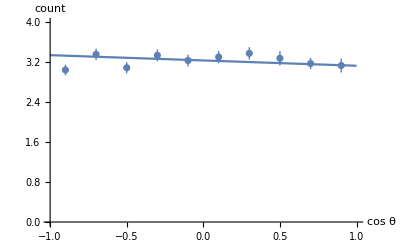

```mathematica
Show[ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}],
Plot[f1[ArcCos[t]],{t,-1,1},PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0}]]
```

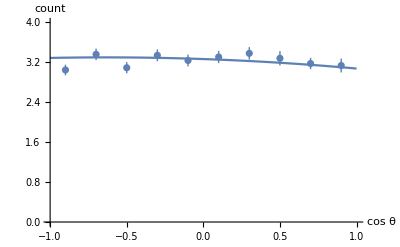

```mathematica
Show[ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}],
Plot[f2[ArcCos[t]],{t,-1,1},PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0}]]
```

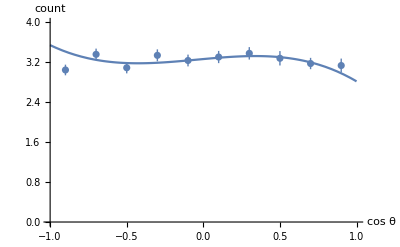

```mathematica
Show[ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}],
Plot[f3[ArcCos[t]],{t,-1,1},PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0}]]
```

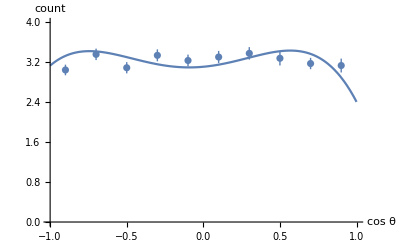

```mathematica
Show[ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}],
Plot[f4[ArcCos[t]],{t,-1,1},PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0}]]
```

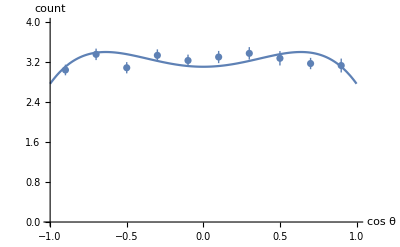

```mathematica
Show[ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}],
Plot[g4[ArcCos[t]],{t,-1,1},PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0}]]
```

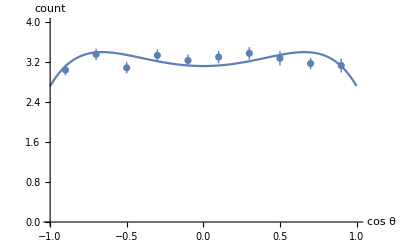

```mathematica
Show[ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}],
Plot[g6[ArcCos[t]],{t,-1,1},PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0}]]
```

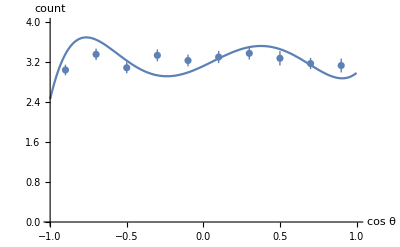

```mathematica
Show[ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}],
Plot[f6[ArcCos[t]],{t,-1,1},PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0}]]
```

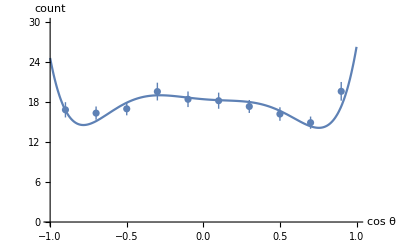

```mathematica
Show[ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,30}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}],
Plot[f6[ArcCos[t]],{t,-1,1},PlotRange->{{-1,1},{0,30}},AxesOrigin->{-1,0}]]
```

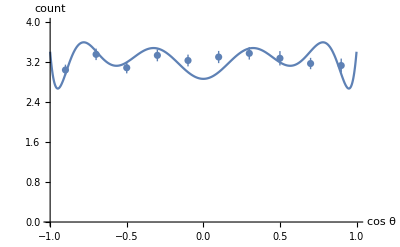

```mathematica
Show[ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}],
Plot[h10[ArcCos[t]],{t,-1,1},PlotRange->{{-1,1},{0,4}},AxesOrigin->{-1,0}]]
```

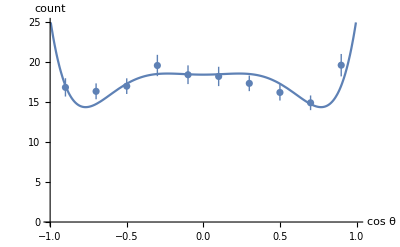

```mathematica
Show[ListPlot[Transpose[{binCenters,binnedMeans}],PlotRange->{{-1,1},{0,25}},AxesOrigin->{-1,0},AxesLabel->{"cos θ", "count"}],
Plot[h6[ArcCos[t]],{t,-1,1},PlotRange->{{-1,1},{0,25}},AxesOrigin->{-1,0}]]
```

```mathematica
h6[z]
```

17.447-0.338458 (-1+3 Cos[z]^2)+0.618142 (3-30 Cos[z]^2+35 Cos[z]^4)+0.236004 (-5+105 Cos[z]^2-315 Cos[z]^4+231 Cos[z]^6)